```mathematica
outputData[graph_]:=Prepend[EdgeList[graph]/.(u_<->v_)->{u-1,v-1},{VertexCount[graph],EdgeCount[graph]}];
outputForMetagraph[graph_]:=Prepend[Flatten[EdgeList[graph]/.(u_<->v_)->{{u-1,v-1},{v-1,u-1}},1],{VertexCount[graph]}]~Join~{{}};
```

```mathematica
graphs=Table[RandomGraph[{n,m}],{n,3,15},{m,n,n(n-1)/2}]//Flatten;
graphs//Length
```

455

```mathematica
Export[
NotebookDirectory[]<>"tests/random-graphs/"<>ToString[VertexCount[#]]<>"-"<>ToString[EdgeCount[#]]<>".txt",
outputData[#],
"Table","FieldSeparators"->" "
]&/@graphs;
```

```mathematica
exportGraph[graph_,name_]:=With[{n=ToString[VertexCount[graph]],m=ToString[EdgeCount[graph]]},
Export[
NotebookDirectory[]<>"tests/"<>name<>"-"<>n<>"-"<>m<>".txt",
outputData[graph],
"Table","FieldSeparators"->" "
];
Export[
NotebookDirectory[]<>"MetagraphMatchingBenchmark/assets/"<>name<>"-"<>n<>"-"<>m<>".txt",
outputForMetagraph[graph],
"Table","FieldSeparators"->" "
];
];
```

```mathematica
bigRandom3=RandomGraph[{10^5,3 10^5}]
exportGraph[bigRandom3,"random"];
```

```mathematica
denseRandom=RandomGraph[{1000,3 10^5}]
exportGraph[denseRandom,"dense-random"];
```

```mathematica
regular3=RandomGraph[DegreeGraphDistribution[Table[3,{i,100000}]]]
exportGraph[regular3,"random-3-regular"];
regular6=RandomGraph[DegreeGraphDistribution[Table[6,{i,100000}]]]
exportGraph[regular6,"random-6-regular"];
```

```mathematica
barabasi3=RandomGraph[BarabasiAlbertGraphDistribution[100000,3]];
exportGraph[barabasi3,"barabasi-albert-3"];
barabasi1=RandomGraph[BarabasiAlbertGraphDistribution[100000,1]];
exportGraph[barabasi1,"barabasi-albert-1"];
```

```mathematica
spatial=RandomGraph[SpatialGraphDistribution[100000,0.005]]
exportGraph[spatial,"spatial2d"];
```

```mathematica
spatial3d=RandomGraph[SpatialGraphDistribution[100000,0.025,3]]
exportGraph[spatial3d,"spatial3d"];
```

```mathematica
Needs["TriangleLink`"]
delaunay2dGraph[numPoints_]:=With[
{points=RandomReal[{0,1},{numPoints,2}]},
{pts,triangles}=TriangleDelaunay[points];
Graph[DeleteDuplicates[Sort/@Flatten[triangles[[All,#]]&/@{{1,2},{2,3},{3,1}},1]]]
];
```

```mathematica
delaunay2d=delaunay2dGraph[100000]
exportGraph[delaunay2d,"delaunay2d"];
```

```mathematica
Needs["TetGenLink`"]
delaunay3dGraph[numPoints_]:=With[
{points=RandomReal[{0,1},{numPoints,3}]},
{pts,tetrahedra}=TetGenDelaunay[points];
Graph[DeleteDuplicates[Sort/@Flatten[tetrahedra[[All,#]]&/@{{1,2},{2,3},{3,1},{1,4},{2,4},{3,4}},1]]]
];
```

```mathematica
delaunay3d=delaunay3dGraph[100000]
exportGraph[delaunay3d,"delaunay3d"];
```

```mathematica
iterateGraph[graph_]:=With[{edgeList=EdgeList[graph]/.(u_<->v_)->{u,v},n=VertexCount[graph],m=EdgeCount[graph]},
Graph[Flatten[Table[edgeList+i n-n,{i,n}],1]~Join~(edgeList*n-n+RandomInteger[{1,n},{m,2}])]
];
```

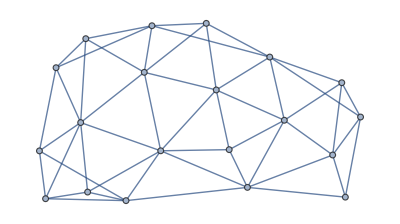

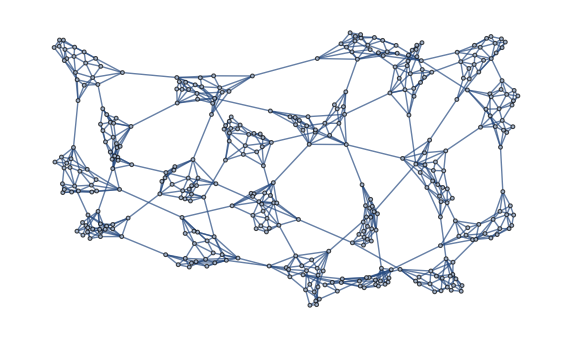

```mathematica
g=delaunay2dGraph[20]
iterateGraph[g]
```

```mathematica
iterDelaunay=iterateGraph[delaunay2dGraph[300]]
exportGraph[iterDelaunay,"iterated-delaunay"];
```

```mathematica
iterRandom=iterateGraph[RandomGraph[{300,1000}]]
exportGraph[iterRandom,"iterated-random"];
```

```mathematica
honeycombGraph[rows_,columns_]:=With[{n=Quotient[columns,2]*2+1,m=rows},
Graph@Flatten[
Table[2i-1+2(n+1)(j-1)<->2i+2(n+1)(j-1),{j,m+1},{i,Quotient[n,2]+1}]~Join~
Table[2i-1+2(n+1)j-n<->2i+2(n+1)j-n,{j,m},{i,Quotient[n,2]}]~Join~
Table[i+(n+1) j-n-1<->i+(n+1) j,{j,2m},{i,n+1}]~Join~
Table[2i+2(n+1) (j-1)<->2i+2(n+1)j,{j,m},{i,Quotient[n,2]+1}]~Join~
Table[2i+2(n+1) (j-1)+n+2<->2i+2(n+1)j+n+2,{j,m-1},{i,Quotient[n,2]}]~Join~
Table[(n+1)(2m+1)+2i-1<->2i,{i,Quotient[n,2]+1}]~Join~
Table[(n+1)(2m+1)+2i<->2i+n+2,{i,Quotient[n,2]}]~Join~
Table[(n+1)(2m+1)+n+m+2i-2<->(n+1)(2m+1)-2i+2,{i,Quotient[n,2]+1}]~Join~
Table[(n+1)(2m+1)+n+m+2i+1-2<->(n+1)(2m+1)-n-2i,{i,Quotient[n,2]}]~Join~
Table[(n+1)(2m+1)+n+j<->2(n+1)j+n+1,{j,m-1}]~Join~
Table[(n+1)(2m+1)+2n+m+j-1<->(n+1)(2m+1)-2(n+1)j+1,{j,m}]
]
]
```

```mathematica
honeycomb=honeycombGraph[250,250]
exportGraph[honeycomb,"honeycomb"];
```

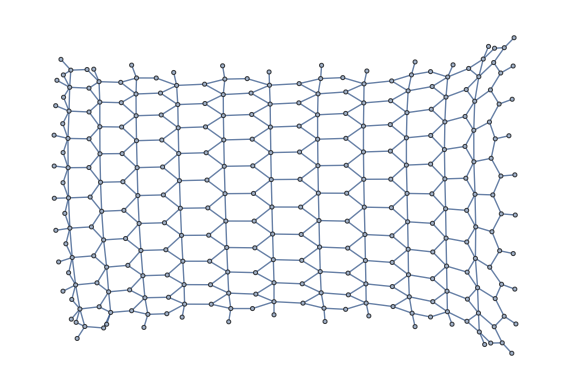

```mathematica
honeycombGraph[10,10]
```